## Funciones

```mathematica
(* Reglas como Subscript[regla, estados, vecinos] *)
CaArray[ca_Subscript,s_,t_]:=CellularAutomaton[{ca[[1]],ca[[2]],(ca[[3]]-1)/2},s,t]

MakeGraph[ca_Subscript,spaceSize_]:=Module[{inits},
  inits=Tuples[Range[0,ca[[2]]-1],spaceSize];
  Graph[
   Map[FromDigits[#[[1]],ca[[2]]]->FromDigits[#[[2]],ca[[2]]] &,(CaArray[ca,#,1] & /@ inits)],
   VertexLabels->Automatic]
  ]
```

```mathematica
(* Grafo cuotientado por rotaciones: cada nodo es una clase de rotaciones ciclicas, representada por su rotacion minima *)
RotClass[state_List]:=First[Sort[NestList[RotateLeft,state,Length[state]-1]]]

MakeGraphRot[ca_Subscript,spaceSize_]:=Module[{classes},
  classes=DeleteDuplicates[RotClass /@ Tuples[Range[0,ca[[2]]-1],spaceSize]];
  Graph[(FromDigits[RotClass[#[[1]]],ca[[2]]]->FromDigits[RotClass[#[[2]]],ca[[2]]] &) /@ (CaArray[ca,#,1] &) /@ classes,
   VertexLabels->Automatic]
  ]
```

```mathematica
(* GPU: la RTX 5080 debe declararse como sm_120 (Wolfram 15 la detecta mal como sm_12) *)
cudaSession=StartExternalSession["CUDA"];

(* Un hilo por configuracion: calcula el indice de su sucesor (misma numeracion que MakeGraph) *)
succKernel=ExternalEvaluate[cudaSession,ExternalOperation["Function",
   Function[{Typed[out,"CArray"::["Integer32"]],Typed[tab,"CArray"::["Integer32"]],Typed[pw,"CArray"::["Integer64"]],
     Typed[k,"MachineInteger"],Typed[r,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
    Module[{id,new,v,cell,dig},
     id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
     If[id<total,
      new=0;
      Do[
       v=0;
       Do[
        cell=Mod[i+d,n];
        dig=Mod[Quotient[id,FromRawPointer[pw,cell]],k];
        v=v*k+dig,{d,-r,r}];
       new=new*k+FromRawPointer[tab,v],{i,0,n-1}];
      ToRawPointer[out,id,Cast[new,"Integer32","CCast"]]];
     ]],
   "CUDAArchitecture"->"sm_120"]];
```

```mathematica
(* Arreglo de sucesores (0-indexado) como NumericArray Integer32; n = numero de celulas.
   Sin temporales de 64 bits: los ceros se arman duplicando con Join y se descarga con NumericArray[out] sin tipo *)
ZerosInt32[total_Integer]:=Module[{z=NumericArray[ConstantArray[0,Min[total,2^20]],"Integer32"]},
  While[Length[z]<total,z=Join[z,z]]; z]

SuccessorArrayGPU[ca_Subscript,n_Integer]:=Module[{k=ca[[2]],m=ca[[3]],total,tab,pw,out},
  total=k^n;
  tab=GPUArray[NumericArray[Reverse[IntegerDigits[ca[[1]],k,k^m]],"Integer32"]];
  pw=GPUArray[NumericArray[k^Range[n-1,0,-1],"Integer64"]];
  out=GPUArray[ZerosInt32[total]];
  succKernel[out,tab,pw,k,(m-1)/2,n,total];
  NumericArray[out]
  ]
```

```mathematica
(* Histograma de ciclos {{longitud, numero de ciclos}, ...} de un grafo funcional (CPU compilado).
   Memoria: 4 bytes por configuracion, valido hasta 2^31 configuraciones.
   stamp (32 bits): 0 = sin visitar; el recorrido s se marca con s - 2^31 - 1 (rango [-2^31, -1]).
   Longitudes <= 2^20 se cuentan en un arreglo; las mayores (a lo mas n/2^20 ciclos) en una lista aparte. *)
cycleHistogramC=FunctionCompile[
   Function[{Typed[succ,"NumericArray"::["Integer32",1]]},
    Module[{n=Length[succ],stamp,lmax=1048576,cnt,big,nb=0,w,v,len,tag,nd=0,res,j=0,bigS},
     stamp=CreateTypeInstance["CArray"::["Integer32"],n];
     Do[ToRawPointer[stamp,i0,Cast[0,"Integer32","CCast"]],{i0,0,n-1}];
     cnt=ConstantArray[0,lmax];
     big=ConstantArray[0,Quotient[n,lmax]+1];
     Do[
      If[FromRawPointer[stamp,s-1]==Cast[0,"Integer32","CCast"],
       tag=Cast[s-2147483649,"Integer32","CCast"];
       w=s;
       While[FromRawPointer[stamp,w-1]==Cast[0,"Integer32","CCast"],
        ToRawPointer[stamp,w-1,tag]; w=succ[[w]]+1];
       If[FromRawPointer[stamp,w-1]==tag,
        len=1; v=succ[[w]]+1;
        While[v!=w,len++; v=succ[[v]]+1];
        If[len<=lmax,cnt[[len]]++,nb++; big[[nb]]=len]]],
      {s,n}];
     DeleteObject[stamp];
     Do[If[cnt[[l]]>0,nd++],{l,lmax}];
     bigS=Sort[Take[big,nb]];
     Do[If[i==1||bigS[[i]]!=bigS[[i-1]],nd++],{i,nb}];
     res=ConstantArray[0,2 nd];
     Do[If[cnt[[l]]>0,res[[2 j+1]]=l; res[[2 j+2]]=cnt[[l]]; j++],{l,lmax}];
     Do[If[i==1||bigS[[i]]!=bigS[[i-1]],res[[2 j+1]]=bigS[[i]]; res[[2 j+2]]=1; j++,res[[2 j]]++],{i,nb}];
     res]]];

CycleHistogram[ca_Subscript,n_Integer]:=<|"Nodes"->ca[[2]]^n,"Cycles"->Partition[cycleHistogramC[SuccessorArrayGPU[ca,n]],2]|>
```

```mathematica
(* Un hilo por configuracion: calcula su representante (rotacion de valor minimo) *)
rotKernel=ExternalEvaluate[cudaSession,ExternalOperation["Function",
   Function[{Typed[out,"CArray"::["Integer32"]],Typed[k,"MachineInteger"],Typed[top,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
    Module[{id,x,best},
     id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
     If[id<total,
      x=0; best=0;
      x=x+id; best=best+id;
      Do[x=Mod[x,top]*k+Quotient[x,top]; If[x<best,best=x],{i,1,n-1}];
      ToRawPointer[out,id,Cast[best,"Integer32","CCast"]]];
     ]],
   "CUDAArchitecture"->"sm_120"]];

RotationClassGPU[ca_Subscript,n_Integer]:=Module[{k=ca[[2]],total,out},
  total=k^n;
  out=GPUArray[NumericArray[ConstantArray[0,total],"Integer32"]];
  rotKernel[out,k,k^(n-1),n,total];
  NumericArray[out,"Integer32"]
  ]

(* Igual que cycleHistogramC, pero recorre solo representantes: sucesor de la clase = clase del sucesor *)
cycleHistogramRotC=FunctionCompile[
   Function[{Typed[succ,"NumericArray"::["Integer32",1]],Typed[canon,"NumericArray"::["Integer32",1]]},
    Module[{n=Length[succ],stamp,nc=0,nodes=0,w,v,len,cyc,j=0,nd=0,lens,cnts},
     stamp=ConstantArray[0,n];
     Do[
      If[canon[[s]]+1==s,
       nodes++;
       If[stamp[[s]]==0,
        w=s;
        While[stamp[[w]]==0,stamp[[w]]=s; w=canon[[succ[[w]]+1]]+1];
        If[stamp[[w]]==s,
         len=1; v=canon[[succ[[w]]+1]]+1;
         While[v!=w,len++; v=canon[[succ[[v]]+1]]+1];
         stamp[[w]]=-len; nc++]]],
      {s,n}];
     cyc=ConstantArray[0,nc];
     Do[If[stamp[[s]]<0,j++; cyc[[j]]=-stamp[[s]]],{s,n}];
     cyc=Sort[cyc];
     lens=ConstantArray[0,nc]; cnts=ConstantArray[0,nc];
     Do[If[nd>0&&lens[[nd]]==cyc[[i]],cnts[[nd]]++,nd++; lens[[nd]]=cyc[[i]]; cnts[[nd]]=1],{i,nc}];
     {nodes,Transpose[{Take[lens,nd],Take[cnts,nd]}]}]]];

(* Mismo formato que CycleHistogram; "Nodes" = numero de clases de rotacion *)
CycleHistogramRot[ca_Subscript,n_Integer]:=With[{r=cycleHistogramRotC[SuccessorArrayGPU[ca,n],RotationClassGPU[ca,n]]},
  <|"Nodes"->r[[1]],"Cycles"->r[[2]]|>]
```

```mathematica
(* Momentos espectrales: m_j = fraccion de configuraciones cuyo ciclo divide a j *)
SpectralMomentsHistogram[h_Association,kmax_Integer]:=With[{L=h["Cycles"][[All,1]],c=h["Cycles"][[All,2]]},
  N[Table[Total[L*c*Boole[Divisible[j,L]]],{j,kmax}]/h["Nodes"]]]

SpectralMomentsHistogramDistance[kmax_Integer][h1_Association,h2_Association]:=
 CosineDistance[SpectralMomentsHistogram[h1,kmax],SpectralMomentsHistogram[h2,kmax]]
```

```mathematica
(* Eigenvalores = raices de la unidad de cada ciclo + ceros.
   Corridas {angulo t en [0,1), multiplicidad} en orden canonico: modulo, Re y Im descendentes *)
EigenAngleRuns[h_Association]:=Module[{c=h["Cycles"],ds,mult},
  ds=Union @@ (Divisors /@ c[[All,1]]);
  mult=AssociationMap[Function[d,Total[Select[c,Divisible[#[[1]],d] &][[All,2]]]],ds];
  SortBy[Flatten[Table[With[{m=mult[d]},{#,m} & /@ (Select[Range[0,d-1],CoprimeQ[#,d] &]/d)],{d,ds}],1],
   {Min[#[[1]],1-#[[1]]] &,Boole[#[[1]]>1/2] &}]]

(* Vector explicito {Re, Im, Re, Im, ...} (solo para espacios pequenos) *)
EigenvaluesHistogram[h_Association]:=With[{runs=EigenAngleRuns[h]},
  Join[N@Flatten[Table[ConstantArray[{Cos[2 Pi r[[1]]],Sin[2 Pi r[[1]]]},r[[2]]],{r,runs}]],
   ConstantArray[0.,2 (h["Nodes"]-Total[runs[[All,2]]])]]]

(* Distancia coseno entre vectores de eigenvalores, sin construirlos *)
EigenvaluesHistogramDistance[h1_Association,h2_Association]:=Module[{r1=EigenAngleRuns[h1],r2=EigenAngleRuns[h2],i=1,j=1,a,b,ov,dot=0.},
  a=r1[[1,2]]; b=r2[[1,2]];
  While[i<=Length[r1]&&j<=Length[r2],
   ov=Min[a,b];
   dot += ov*N[Cos[2 Pi (r1[[i,1]]-r2[[j,1]])]];
   a -= ov; b -= ov;
   If[a==0,i++; If[i<=Length[r1],a=r1[[i,2]]]];
   If[b==0,j++; If[j<=Length[r2],b=r2[[j,2]]]]];
  1-dot/Sqrt[Total[r1[[All,2]]]*Total[r2[[All,2]]]]]
```

```mathematica
GroupRelations[rels_Association,types_ : All,extra_List : {}]:=Module[{keys,edges},
  keys=If[types===All,Keys[rels],Intersection[Flatten[{types}],Keys[rels]]];
  edges=UndirectedEdge @@@ Flatten[Lookup[rels,keys,{}]];
  SortBy[Sort /@ ConnectedComponents[Graph[extra,edges]],{-Length[#] &,First}]
  ]

(* Se aplica DESPUES de agrupar: conserva solo las ECA (2 estados, 3 vecinos) y descarta los grupos vacios *)
OnlyECA[groups_List]:=DeleteCases[Cases[#,Subscript[_,2,3]] & /@ groups,{}]

ecaRules=Table[Subscript[r,2,3],{r,0,255}];
```

## Ejecución

```mathematica
ecaHist=AssociationMap[Function[n,Table[CycleHistogram[Subscript[r,2,3],n],{r,0,255}]],Range[1,25]];
ecaHistRot=AssociationMap[Function[n,Table[CycleHistogramRot[Subscript[r,2,3],n],{r,0,255}]],Range[1,25]];
Iconize[{ecaHist,ecaHistRot},"Histogramas de ciclos ECA n = 1..25 {crudo, rotaciones}"]
```

```mathematica
{ecaHist,ecaHistRot}=;
```

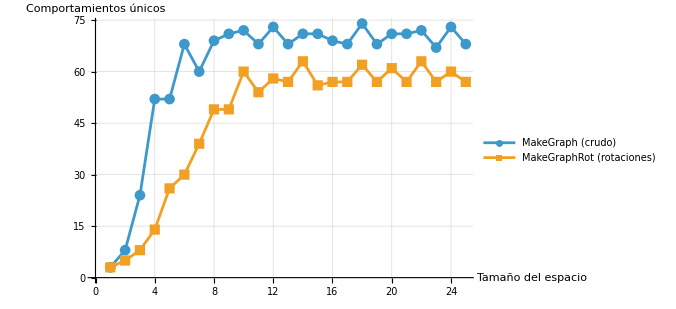

```mathematica
uniq=Length@DeleteDuplicates[#] & /@ Values[ecaHist];
uniqRot=Length@DeleteDuplicates[#] & /@ Values[ecaHistRot];
ListLinePlot[{uniq,uniqRot},DataRange->{1,25},PlotMarkers->Automatic,
 PlotLegends->{"MakeGraph (crudo)","MakeGraphRot (rotaciones)"},
 AxesLabel->{"Tamaño del espacio","Comportamientos únicos"},PlotRange->{0,Automatic},GridLines->Automatic,ImageSize->500]
```

```mathematica
relations=;
```

## Agrupación de relaciones

```mathematica
gAll=OnlyECA[gruposTodos];
gAAll=OnlyECA[gruposInvMir];
```

```mathematica
gEcahist=Subscript[#,2,3]&/@#&/@
Values[GroupBy[Thread[Range[0,255]->ecaHist[18]],Last->First]];
gEcahistRot=Subscript[#,2,3]&/@#&/@
Values[GroupBy[Thread[Range[0,255]->ecaHistRot[22]],Last->First]];
```

```mathematica
UniqueElements[{gAll,gAAll}];
```

```mathematica
Length[#]&/@{gAll,gAAll,gEcahist,gEcahistRot}
```

{81,88,74,63}

VAMOS A USA gAll. Las agrupaciones obtenidas por las reducciones de estados son validas, las vamos a considerar dentro de la misma clasificación. Ahora el momento es comparar gEcahist y gEcahistrot

```mathematica
UniqueElements[{gAll,gEcahist}];
```

```mathematica
(*Para cada grupo de "grandes":que grupos de "chicos" caen completos dentro,si lo cubren exactamente,y cuales lo cruzan parcialmente*)Descomponer[grandes_List,chicos_List]:=Table[With[{dentro=Select[chicos,SubsetQ[g,#]&]},<|"Grupo"->g,"Partes"->dentro,"NPartes"->Length[dentro],"Exacto"->Sort[Flatten[dentro]]===Sort[g],"Cruzados"->Select[chicos,IntersectingQ[g,#]&&!SubsetQ[g,#]&&!SubsetQ[#,g]&]|>],{g,grandes}];

dA=Descomponer[gAll,gEcahist];   (*gAll partido en grupos de gEcahist*)
dE=Descomponer[gEcahist,gAll];   (*gEcahist partido en grupos de gAll*)

Select[dA,#Exacto&&#NPartes>1&]   ;(*grupos de gAll hechos de varios de gEcahist*)
Select[dE,#Exacto&&#NPartes>1&]   ;(*grupos de gEcahist hechos de varios de gAll*)
Select[dA,#Cruzados=!={}&]          ;(*traslapes parciales:ninguno contiene al otro*)
```

```mathematica
Select[dA,#Exacto&&#NPartes>1&]
```

{<|Grupo→{3_(2,3),5_(2,3),17_(2,3),63_(2,3),95_(2,3),119_(2,3)},Partes→{{3_(2,3),17_(2,3),63_(2,3),119_(2,3)},{5_(2,3),95_(2,3)}},NPartes→2,Exacto→True,Cruzados→{}|>,<|Grupo→{60_(2,3),90_(2,3),102_(2,3),153_(2,3),165_(2,3),195_(2,3)},Partes→{{60_(2,3),102_(2,3),153_(2,3),195_(2,3)},{90_(2,3),165_(2,3)}},NPartes→2,Exacto→True,Cruzados→{}|>}

Aqui tenemos resultados.

```mathematica
(*Comportamientos que coinciden*)
Flatten[Intersection[gAll,gEcahist]]//Length
(*Comportamientos similiares de gAll que gEcaHist clasifica como diferentes*)
Flatten[Select[dA,#Exacto&&#NPartes>1&][[;;,"Grupo"]]]//Length
(*Comportamientos diferentes de gAll que gEcaHist clasifica como iguales*)
Flatten[Select[dE,#Exacto&&#NPartes>1&][[;;,"Grupo"]]]//Length
(*Comportamientos cruzados,es decir, diferentes comportamientos combinados de ambos*)
Flatten[Select[dA,#Cruzados=!={}&][[;;,"Grupo"]]]//Length

Flatten[Select[dE,#Cruzados=!={}&][[;;,"Grupo"]]]//Length
```

160

12

56

24

16

```mathematica
Position[gEcahist,Subscript[4,2,3]]
```

{{5,1}}

```mathematica
gAll[[47]]
gEcahist[[5]]
```

{4_(2,3),223_(2,3)}

{4_(2,3),12_(2,3),68_(2,3),207_(2,3),221_(2,3),223_(2,3)}

```mathematica
160+12+56+24
```

252

```mathematica
Select[dA,#Cruzados=!={}&]
```

{<|Grupo→{10_(2,3),12_(2,3),34_(2,3),48_(2,3),68_(2,3),80_(2,3),175_(2,3),187_(2,3),207_(2,3),221_(2,3),243_(2,3),245_(2,3)},Partes→{{10_(2,3),80_(2,3),175_(2,3),245_(2,3)},{34_(2,3),48_(2,3),187_(2,3),243_(2,3)}},NPartes→2,Exacto→False,Cruzados→{{4_(2,3),12_(2,3),68_(2,3),207_(2,3),221_(2,3),223_(2,3)}}|>,<|Grupo→{136_(2,3),160_(2,3),192_(2,3),238_(2,3),250_(2,3),252_(2,3)},Partes→{{160_(2,3),250_(2,3)}},NPartes→1,Exacto→False,Cruzados→{{128_(2,3),136_(2,3),192_(2,3),238_(2,3),252_(2,3),254_(2,3)}}|>,<|Grupo→{15_(2,3),51_(2,3),85_(2,3)},Partes→{{51_(2,3)}},NPartes→1,Exacto→False,Cruzados→{{15_(2,3),85_(2,3),170_(2,3),240_(2,3)}}|>,<|Grupo→{170_(2,3),204_(2,3),240_(2,3)},Partes→{{204_(2,3)}},NPartes→1,Exacto→False,Cruzados→{{15_(2,3),85_(2,3),170_(2,3),240_(2,3)}}|>}

### Comparación de gAll contra los histogramas de ciclos

CompararClasificaciones une en un bloque todos los grupos de ambas clasificaciones que comparten reglas, y clasifica cada bloque según cuántos grupos tiene de cada lado. Así cada regla cae en exactamente una de cuatro categorías y la suma siempre da 256.

Coinciden: un grupo de A y un grupo de B, idénticos.

A junta, B separa: un grupo de A partido en varios grupos de B.

A separa, B junta: varios grupos de A unidos en un grupo de B.

Cruzados: varios grupos de cada lado que se traslapan sin que ninguno contenga al otro.

```mathematica
(* Une grupos de ambas clasificaciones que comparten reglas; cada bloque se clasifica
   segun cuantos grupos de cada lado contiene. A = primera lista, B = segunda *)
CompararClasificaciones[gA_List,gB_List]:=Module[{nodos,aristas,comps},
  nodos=Join[Thread[{"A",Range[Length[gA]]}],Thread[{"B",Range[Length[gB]]}]];
  aristas=Flatten[Table[If[IntersectingQ[gA[[i]],gB[[j]]],{"A",i} <-> {"B",j},Nothing],
     {i,Length[gA]},{j,Length[gB]}]];
  comps=ConnectedComponents[Graph[nodos,aristas]];
  Map[Function[c,With[{a=gA[[Cases[c,{"A",i_}:>i]]],b=gB[[Cases[c,{"B",j_}:>j]]]},
      <|"Tipo"->Which[Length[a]==1&&Length[b]==1,"Coinciden",
         Length[b]>1&&Length[a]==1,"A junta, B separa",
         Length[a]>1&&Length[b]==1,"A separa, B junta",
         True,"Cruzados"],
       "Reglas"->Sort[Flatten[a]],"GruposA"->a,"GruposB"->b|>]],comps]];

bloques=CompararClasificaciones[gAll,gEcahist];
cuenta=Length@*Flatten /@ GroupBy[bloques,#Tipo &,#[[All,"Reglas"]] &]
Total[cuenta]
```

<|Cruzados→28,A separa, B junta→56,A junta, B separa→12,Coinciden→160|>

256

Conteo de las cuatro categorías para cada tamaño del espacio, sin cocientar (ecaHist) y cocientado por rotaciones (ecaHistRot), siempre contra gAll.

```mathematica
(* Agrupa las 256 ECA por histograma identico, en la notacion Subscript[r, 2, 3] *)
GruposHist[h_List]:=Map[Subscript[#,2,3] &,Values[GroupBy[Thread[Range[0,255]->h],Last->First]],{2}];

categorias={"Coinciden","A junta, B separa","A separa, B junta","Cruzados"};
etiquetas={"Coinciden","gAll junta, histograma separa","gAll separa, histograma junta","Cruzados"};

(* Numero de reglas en cada categoria al comparar gAll contra una clasificacion *)
ConteoCategorias[gB_List]:=With[{c=Length@*Flatten /@ GroupBy[CompararClasificaciones[gAll,gB],#Tipo &,#[[All,"Reglas"]] &]},
   Lookup[c,categorias,0]];

conteoRaw=Table[ConteoCategorias[GruposHist[ecaHist[n]]],{n,1,25}];
conteoRot=Table[ConteoCategorias[GruposHist[ecaHistRot[n]]],{n,1,25}];

PlotCategorias[datos_,titulo_]:=ListLinePlot[Transpose[datos],DataRange->{1,25},
   PlotMarkers->Automatic,PlotLegends->etiquetas,PlotLabel->titulo,
   AxesLabel->{"Tamaño del espacio","Reglas"},PlotRange->{0,256},GridLines->Automatic,ImageSize->500];
```

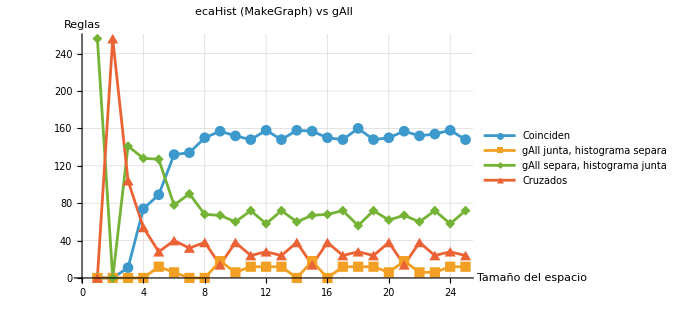

```mathematica
PlotCategorias[conteoRaw,"ecaHist (MakeGraph) vs gAll"]
```

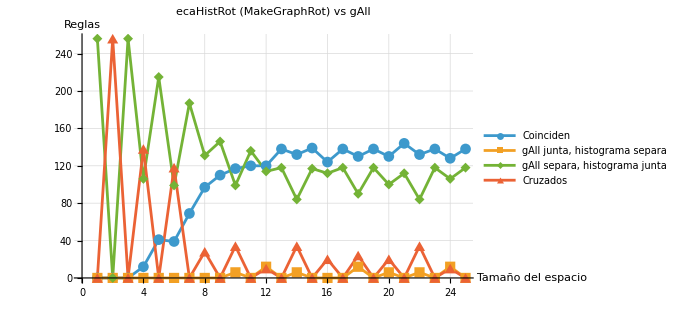

```mathematica
PlotCategorias[conteoRot,"ecaHistRot (MakeGraphRot) vs gAll"]
```

## Periodicidad en el tamaño del espacio

Resultados completos, tablas y conclusiones en resultados_periodicidad_histogramas.md (carpeta del proyecto). Esta sección guarda el código y carga los datos que se calcularon fuera del notebook. Requiere haber evaluado las secciones anteriores (ecaHist, gAll, gruposInvMirECA, CompararClasificaciones, GruposHist, ConteoCategorias, PlotCategorias).

### Datos calculados fuera del notebook

ecaHist_26_28.wl y ecaHist_31.wl: histogramas ECA con 26, 27, 28 y 31 células. hist22.wl: las 16 reglas de 2 estados y 2 vecinos, sin cocientar (1 a 31) y con rotaciones (1 a 29).

```mathematica
dirProyecto="/home/rediax/Documents/Projects/CA-Similarity-Index/";
ecaHist=Join[ecaHist,Get[dirProyecto <> "ecaHist_26_28.wl"],Get[dirProyecto <> "ecaHist_31.wl"]];
hist22=Get[dirProyecto <> "hist22.wl"];
raw22=hist22["raw"];
rot22=hist22["rot"];
Keys /@ {ecaHist,raw22,rot22}
```

{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,31},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31},{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29}}

### Funciones auxiliares

```mathematica
(* Grafos de transicion de varias reglas con i celulas. rot = True usa MakeGraphRot *)
PlotRulesGraph[rules_List,i_Integer,rot_ : False]:=Grid[Partition[
    Table[Labeled[
      Graph[If[rot,MakeGraphRot,MakeGraph][r,i],VertexLabels->If[i<=4,Automatic,None],VertexSize->Small,ImageSize->220],
      Row[{"Regla ",r[[1]]}],Top],{r,rules}],UpTo[3]],Frame->All];

(* Una regla representativa por grupo inverse/mirror: en ECA comparten histograma (verificado n = 1..25) *)
repDe=Association[Flatten[Thread[#->First[#]] & /@ gruposInvMirECA]];
ExpandirReps[h_Association]:=Table[h[repDe[Subscript[r,2,3]]],{r,0,255}];

(* Particion por histograma para n celulas, y la misma sin las reglas lineales/afines *)
ParticionECA[n_]:=Sort[Sort /@ GruposHist[ecaHist[n]]];
linealesECA=Subscript[#,2,3] & /@ {0,60,90,102,150,170,204,240,255,195,165,153,105,85,51,15};
ParticionSinLineales[n_]:=Sort[DeleteCases[Sort /@ (Complement[#,linealesECA] & /@ ParticionECA[n]),{}]];

(* Familias de tamanos con exactamente la misma particion *)
FamiliasECA[ns_List]:=Values[GroupBy[ns,ParticionECA]];
FamiliasSinLineales[ns_List]:=Values[GroupBy[ns,ParticionSinLineales]];
```

```mathematica
FamiliasSinLineales[Join[Range[1,28],{31}]]
```

{{1},{2},{3},{4},{5},{6},{7},{8,10,14,16,20,22,26,28},{9,15,21,27},{11,13,17,19,23,25,31},{12,18,24}}

### Espacio de 2 estados y 2 vecinos

Con 2 vecinos la vecindad de la celda i es (i - 1, i), que no es simetrica. El kernel succKernel solo acepta vecindades -r..r, asi que succKernelLH recibe el rango lo..hi (m impar: -r..r; m = 2: -1..0).

```mathematica
(* Un hilo por configuracion; vecindad = celdas i+lo .. i+hi *)
succKernelLH=ExternalEvaluate[cudaSession,ExternalOperation["Function",
    Function[{Typed[out,"CArray"::["Integer32"]],Typed[tab,"CArray"::["Integer32"]],Typed[pw,"CArray"::["Integer64"]],
      Typed[k,"MachineInteger"],Typed[lo,"MachineInteger"],Typed[hi,"MachineInteger"],Typed[n,"MachineInteger"],Typed[total,"MachineInteger"]},
     Module[{id,new,v,cell,dig},
      id=LibraryFunction["BlockDimensions.x"][]*LibraryFunction["BlockID.x"][]+LibraryFunction["ThreadID.x"][];
      If[id<total,
       new=0;
       Do[
        v=0;
        Do[
         cell=Mod[i+d,n];
         dig=Mod[Quotient[id,FromRawPointer[pw,cell]],k];
         v=v*k+dig,{d,lo,hi}];
        new=new*k+FromRawPointer[tab,v],{i,0,n-1}];
       ToRawPointer[out,id,Cast[new,"Integer32","CCast"]]];
      ]],
    "CUDAArchitecture"->"sm_120"]];

SuccessorArrayGPULH[ca_Subscript,n_Integer]:=Module[{k=ca[[2]],m=ca[[3]],total,tab,pw,out},
   total=k^n;
   tab=GPUArray[NumericArray[Reverse[IntegerDigits[ca[[1]],k,k^m]],"Integer32"]];
   pw=GPUArray[NumericArray[k^Range[n-1,0,-1],"Integer64"]];
   out=GPUArray[ZerosInt32[total]];
   succKernelLH[out,tab,pw,k,-Ceiling[(m-1)/2],Floor[(m-1)/2],n,total];
   NumericArray[out]];

CycleHistogramLH[ca_Subscript,n_Integer]:=<|"Nodes"->ca[[2]]^n,"Cycles"->Partition[cycleHistogramC[SuccessorArrayGPULH[ca,n]],2]|>;
CycleHistogramRotLH[ca_Subscript,n_Integer]:=With[{r=cycleHistogramRotC[SuccessorArrayGPULH[ca,n],RotationClassGPU[ca,n]]},
   <|"Nodes"->r[[1]],"Cycles"->r[[2]]|>];
```

```mathematica
rules22=Table[Subscript[r,2,2],{r,0,15}];
gAll22=DeleteCases[Cases[#,Subscript[_,2,2]] & /@ GroupRelations[relations,All,Join[ecaRules,rules22]],{}];
Grupos22[h_List]:=Map[Subscript[#,2,2] &,Values[GroupBy[Thread[Range[0,15]->h],Last->First]],{2}];
Conteo22[gB_List]:=With[{c=Length@*Flatten /@ GroupBy[CompararClasificaciones[gAll22,gB],#Tipo &,#[[All,"Reglas"]] &]},
   Lookup[c,categorias,0]];
conteo22raw=Table[Conteo22[Grupos22[raw22[n]]],{n,1,31}];
conteo22rot=Table[Conteo22[Grupos22[rot22[n]]],{n,1,29}];
PlotCategorias22[datos_,titulo_,nmax_]:=ListLinePlot[Transpose[datos],DataRange->{1,nmax},
   PlotMarkers->Automatic,PlotLegends->etiquetas,PlotLabel->titulo,
   AxesLabel->{"Tamaño del espacio","Reglas"},PlotRange->{0,16},GridLines->Automatic,ImageSize->500];
```

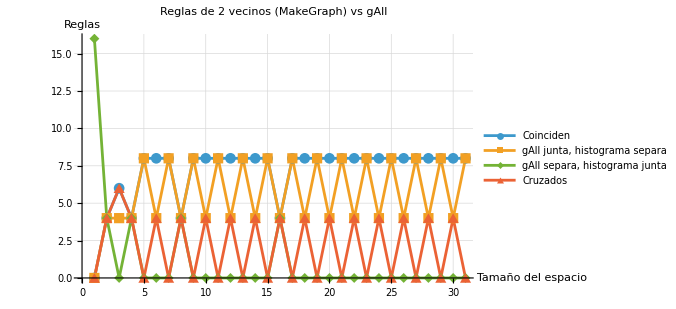

```mathematica
PlotCategorias22[conteo22raw,"Reglas de 2 vecinos (MakeGraph) vs gAll",31]
```

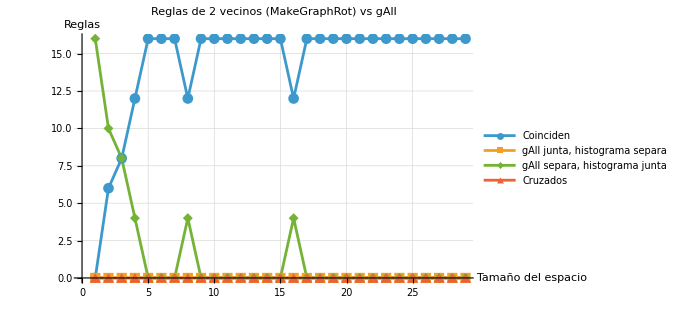

```mathematica
PlotCategorias22[conteo22rot,"Reglas de 2 vecinos (MakeGraphRot) vs gAll",29]
```